```mathematica
(*Arbitraty dimension calcualtion*)
```

```mathematica
dim1=2;
vr1={t,x};
g1=L^2/Cos[x]^2({{-A[x] ⅇ^(-2δ[x]), 0}, {0, 1/A[x]}});
ω[t_,x_]:=Log[L Tan[x]]
```

```mathematica
f1=FullSimplify[Inverse[g1]];
G1=FullSimplify[Table[Sum[1/2*f1[[i,l]]*(D[g1[[l,k]], vr1[[j]]]+D[g1[[l,j]], vr1[[k]]]-D[g1[[j,k]], vr1[[l]]]),{l,1,dim1}],{i,1,dim1},{j,1,dim1},{k,1,dim1}]];
Rm1=Simplify[Table[D[G1[[i,k,m]], vr1[[l]]]-D[G1[[i,k,l]], vr1[[m]]]+Sum[G1[[e,k,m]]*G1[[i,e,l]]-G1[[e,k,l]]*G1[[i,e,m]],{e,1,dim1}],{i,1,dim1},{k,1,dim1},{l,1,dim1},{m,1,dim1}]];
Rc1=FullSimplify[Table[Sum[Rm1[[i,k,i,m]],{i,1,dim1}],{k,1,dim1},{m,1,dim1}]];
R1=Simplify[Sum[Rc1[[i,j]]*f1[[i,j]],{i,1,dim1},{j,1,dim1}]];
Ge1=Simplify[Table[Rc1[[i,j]]-1/2*R1*g1[[i,j]],{i,1,dim1},{j,1,dim1}]];
```

```mathematica
D2[f_]:=Table[D[D[f, vr1[[j]]], vr1[[i]]]-Sum[G1[[k,i,j]]D[f, vr1[[k]]],{k,1,dim1}],{i,1,dim1},{j,1,dim1}]
DD[f_]:=Table[(D[f, vr1[[i]]])(D[f, vr1[[j]]]),{i,1,dim1},{j,1,dim1}]
```

```mathematica
D2Omega=Simplify[D2[ω[t,x]]];
DalOmega=Simplify[Tr[f1.D2Omega]];
DOmegaDOmega=Simplify[DD[ω[t,x]]];
DOmega2=Simplify[Tr[f1.DOmegaDOmega]];
```

```mathematica
GeTX=Simplify[Ge1-(d-1)(D2Omega+DOmegaDOmega)+g1((d-1) DalOmega+1/2 d(d-1)DOmega2-1/2(d-1)(d-2)ⅇ^(-2ω[t,x]))];
GeAng=Simplify[ⅇ^(2ω[t,x])((d-2) DalOmega+1/2(d-1)(d-2)DOmega2-1/2 R1)-1/2(d-2)(d-3)];
```

```mathematica
(*Subtracting vacuum energy*)
```

```mathematica
TeTX=Simplify[GeTX-(d(d-1))/(2 L^2)g1];
TeAng=Simplify[GeAng-(d(d-1))/(2 L^2)ⅇ^(2ω[t,x])];
```

```mathematica
(*Checking vanishing of Stress-Energy covariant derivative*)
```

```mathematica
FullSimplify[D[A[x]*TeTX[[2,2]],x]-(d-1)Csc[x]^3 Sec[x]TeAng+1/2 A[x] (2 (-3+2 d+Cos[2 x]) Csc[2 x]+A'[x]/A[x]-2 δ'[x])TeTX[[2,2]]+1/2 ⅇ^(2δ[x])/A[x] (2 Tan[x]+A'[x]/A[x]-2 δ'[x])TeTX[[1,1]]]
```

0

```mathematica
(*Matter part*)
```

```mathematica
$Assumptions={ϕ[x]∈ Reals,ϕ'[x]∈ Reals,t∈Reals,ω∈Reals};
```

```mathematica
Φ[t_,x_]:=ϕ[x] ⅇ^(ⅈ ω t)
```

```mathematica
Lgr2=Simplify[Sum[Conjugate[(D[Φ[t,x], vr1[[k]]])] D[Φ[t,x], vr1[[l]]]f1[[k,l]],{k,1,dim1},{l,1,dim1}]+V[Conjugate[Φ[t,x]] Φ[t,x]]];
TmTX=FullSimplify[Table[Conjugate[(D[Φ[t,x], vr1[[i]]])] D[Φ[t,x], vr1[[j]]]+D[Φ[t,x], vr1[[i]]] Conjugate[(D[Φ[t,x], vr1[[j]]])]-
g1[[i,j]]Lgr2,{i,1,dim1},{j,1,dim1}]];
TuTX=FullSimplify[TmTX.f1];
```

```mathematica
EOMTX=TeTX-κ TmTX;
EOMAng=TeAng+κ Lgr2 ⅇ^(2ω[t,x]);
```

```mathematica
EOMPhi:=ϕ''[x]+(A'[x]/A[x]-δ'[x]+(d-1)/(Sin[x]Cos[x])) ϕ'[x]+1/A[x] (ⅇ^(2δ[x])/A[x] ω^2- L^2/Cos[x]^2 V'[ϕ[x]^2])ϕ[x]
```

```mathematica
(*Checking conservation consistency*)
```

```mathematica
FullSimplify[D[A[x]*EOMTX[[2,2]],x]-(d-1)Csc[x]^3 Sec[x]EOMAng+1/2 A[x] (2 (-3+2 d+Cos[2 x]) Csc[2 x]+A'[x]/A[x]-2 δ'[x])EOMTX[[2,2]]+1/2 ⅇ^(2δ[x])/A[x] (2 Tan[x]+A'[x]/A[x]-2 δ'[x])EOMTX[[1,1]]+2 A[x]ϕ'[x]κ EOMPhi]
```

0

```mathematica
(*Writing out equations*)
```

```mathematica
-Collect[TuTX[[1,1]],Cos[x]^2,Simplify]
```

V[ϕ[x]^2]+(Cos[x]^2 (ⅇ^(2 δ[x]) ω^2 ϕ[x]^2+A[x]^2 ϕ'[x]^2))/(L^2 A[x])

```mathematica
EOMA:=A'[x]+((A[x]-1) (d-2 Cos[x]^2))/(Sin[x]Cos[x])+(2 L^2 Tan[x])/(d-1)κ ρ
EOMdelta:=δ'[x]+(L^2 Tan[x])/((d-1)A[x])κ(ρ+pr)
```

```mathematica
Simplify[(TeTX.f1)[[1,1]]/.Solve[EOMA==0,A'[x]][[1]]]
```

-κ ρ

```mathematica
FullSimplify[(EOMTX[[1,1]]/.Solve[EOMA==0,A'[x]][[1]])/.ρ->Cos[x]^2/L^2(ⅇ^(2 δ[x])/A[x] ω^2 ϕ[x]^2+A[x] ϕ'[x]^2)+V[ϕ[x]^2]]
```

0

```mathematica
FullSimplify[(TeTX.f1)[[2,2]]/.Solve[{EOMA==0,EOMdelta==0},{A'[x],δ'[x]}][[1]]]
```

pr κ

```mathematica
FullSimplify[(EOMTX[[2,2]]/.Solve[{EOMA==0,EOMdelta==0},{A'[x],δ'[x]}][[1]])/.pr->Cos[x]^2/L^2(ⅇ^(2 δ[x])/A[x] ω^2 ϕ[x]^2+A[x] ϕ'[x]^2)-V[ϕ[x]^2]]
```

0

```mathematica
(*Vacuum solutions*)
```

```mathematica
A[x_]:=1-(C[1] Cos[x]^2)/Tan[x]^(d-2)
```

```mathematica
FullSimplify[EOMA/.ρ->0]
```

0

```mathematica
ClearAll[A]
```

```mathematica
(*4D Check*)
```

```mathematica
dim=4;
vr:={t,x,θ,ϕ}
g:=L^2/Cos[x]^2({{-A[x] ⅇ^(-2δ[x]), 0, 0, 0}, {0, 1/A[x], 0, 0}, {0, 0, Sin[x]^2, 0}, {0, 0, 0, Sin[x]^2 Sin[θ]^2}})
```

```mathematica
f=FullSimplify[Inverse[g]];
G=FullSimplify[Table[Sum[1/2*f[[i,l]]*(D[g[[l,k]], vr[[j]]]+D[g[[l,j]], vr[[k]]]-D[g[[j,k]], vr[[l]]]),{l,1,dim}],{i,1,dim},{j,1,dim},{k,1,dim}]];
Rm=Simplify[Table[D[G[[i,k,m]], vr[[l]]]-D[G[[i,k,l]], vr[[m]]]+Sum[G[[e,k,m]]*G[[i,e,l]]-G[[e,k,l]]*G[[i,e,m]],{e,1,dim}],{i,1,dim},{k,1,dim},{l,1,dim},{m,1,dim}]];
Rc=FullSimplify[Table[Sum[Rm[[i,k,i,m]],{i,1,dim}],{k,1,dim},{m,1,dim}]];
R=Simplify[Sum[Rc[[i,j]]*f[[i,j]],{i,1,dim},{j,1,dim}]];
Ge=Simplify[Table[Rc[[i,j]]-1/2*R*g[[i,j]],{i,1,dim},{j,1,dim}]];
Geu=FullSimplify[Ge.f];
```

```mathematica
Te=Simplify[Ge-3/L^2 g];
```

```mathematica
FullSimplify[Te[[1,1]]-TeTX[[1,1]]/.d->3]
```

0

```mathematica
FullSimplify[Te[[2,2]]-TeTX[[2,2]]/.d->3]
```

0

```mathematica
FullSimplify[Te[[3,3]]-TeAng/.d->3]
```

0

```mathematica
$Assumptions={ϕ[x]∈ Reals,ϕ'[x]∈ Reals,t∈Reals,ω∈Reals};
```

```mathematica
Φ[t_,x_]:=ϕ[x] ⅇ^(ⅈ ω t)
```

```mathematica
Lgr=Simplify[Sum[Conjugate[(D[Φ[t,x], vr[[k]]])] D[Φ[t,x], vr[[l]]]f[[k,l]],{k,1,dim},{l,1,dim}]+V[Conjugate[Φ[t,x]] Φ[t,x]]];
T=FullSimplify[Table[Conjugate[(D[Φ[t,x], vr[[i]]])] D[Φ[t,x], vr[[j]]]+D[Φ[t,x], vr[[i]]] Conjugate[(D[Φ[t,x], vr[[j]]])]-
g[[i,j]]Lgr,{i,1,dim},{j,1,dim}]];
Tu=FullSimplify[T.f];
```

```mathematica
Tu//MatrixForm
```

(-(L^2 A[x] V[ϕ[x]^2]+ⅇ^(2 δ[x]) ω^2 Cos[x]^2 ϕ[x]^2+A[x]^2 Cos[x]^2 ϕ'[x]^2)/(L^2 A[x]) | 0 | 0 | 0
0 | -V[ϕ[x]^2]+(Cos[x]^2 (ⅇ^(2 δ[x]) ω^2 ϕ[x]^2+A[x]^2 ϕ'[x]^2))/(L^2 A[x]) | 0 | 0
0 | 0 | -V[ϕ[x]^2]+(Cos[x]^2 (ⅇ^(2 δ[x]) ω^2 ϕ[x]^2-A[x]^2 ϕ'[x]^2))/(L^2 A[x]) | 0
0 | 0 | 0 | -V[ϕ[x]^2]+(Cos[x]^2 (ⅇ^(2 δ[x]) ω^2 ϕ[x]^2-A[x]^2 ϕ'[x]^2))/(L^2 A[x]))

```mathematica
FullSimplify[D[A[x]*Te[[2,2]],x]-2 Csc[x]^3 Sec[x]Te[[3,3]]+1/2 A[x] (4 Cot[x]+2 Tan[x]+A'[x]/A[x]-2 δ'[x])Te[[2,2]]+1/2 ⅇ^(2δ[x])/A[x] (2 Tan[x]+A'[x]/A[x]-2 δ'[x])Te[[1,1]]]
```

0

```mathematica
(*Scalar field exact solution with no backreaction*)
```

```mathematica
FieldEOM[f_]:=D[f,{x,2}]+(d-1)/(Sin[x]Cos[x])D[f,x]+(ω^2- (m^2 L^2)/Cos[x]^2)f
```

```mathematica
e[j_,x_]:=Cos[x]^d JacobiP[j,d/2-1,d/2,Cos[2x]]
```

```mathematica
FullSimplify[(FieldEOM[e[j,x]]/.ω->(d+2j)/.m->0)/.j->5]
```

0

```mathematica
ClearAll[ω]
```

```mathematica
DSolve[FieldEOM[F[x]]==0,F[x],x]
```

{{F[x]→(-1)^(1/4 (d-√(d^2+4 L^2 m^2))) C[1] Cos[x]^(1/2 (d-√(d^2+4 L^2 m^2))) Hypergeometric2F1[d/4-1/4 √(d^2+4 L^2 m^2)-ω/2,d/4-1/4 √(d^2+4 L^2 m^2)+ω/2,1-1/2 √(d^2+4 L^2 m^2),Cos[x]^2]+(-1)^(1/4 (d+√(d^2+4 L^2 m^2))) C[2] Cos[x]^(1/2 (d+√(d^2+4 L^2 m^2))) Hypergeometric2F1[d/4+1/4 √(d^2+4 L^2 m^2)-ω/2,d/4+1/4 √(d^2+4 L^2 m^2)+ω/2,1+1/2 √(d^2+4 L^2 m^2),Cos[x]^2]}}

```mathematica
(*A singular branch*)
```

```mathematica
Assuming[d>0,Refine[Cos[x]^(1/2 (d-√(d^2+4 L^2 m^2))) Hypergeometric2F1[d/4-1/4 √(d^2+4 L^2 m^2)-ω/2,d/4-1/4 √(d^2+4 L^2 m^2)+ω/2,1-1/2 √(d^2+4 L^2 m^2),Cos[x]^2]/.m->0]]
```

Hypergeometric2F1[-ω/2,ω/2,1-d/2,Cos[x]^2]

```mathematica
(*Considering regular branch*)
```

```mathematica
Assuming[d>0,Refine[Cos[x]^(1/2 (d+√(d^2+4 L^2 m^2))) Hypergeometric2F1[d/4+1/4 √(d^2+4 L^2 m^2)-ω/2,d/4+1/4 √(d^2+4 L^2 m^2)+ω/2,1+1/2 √(d^2+4 L^2 m^2),Cos[x]^2]/.m->0]]
```

Cos[x]^d Hypergeometric2F1[d/2-ω/2,d/2+ω/2,1+d/2,Cos[x]^2]

```mathematica
Clear[ω,a,b,c,p]
```

```mathematica
a:=d/4+1/4 √(d^2+4 L^2 m^2)-ω/2
b:=d/4+1/4 √(d^2+4 L^2 m^2)+ω/2
c:=1+1/2 √(d^2+4 L^2 m^2)
p:=1/2 (d+√(d^2+4 L^2 m^2))
```

```mathematica
Series[(Gamma[c]Gamma[c-a-b])/(Gamma[c-a]Gamma[c-b])Hypergeometric2F1[a,b,a+b+1-c,Sin[x]^2]+(Gamma[c]Gamma[a+b-c])/(Gamma[a]Gamma[b])Sin[x]^(2(c-a-b))Hypergeometric2F1[c-a,c-b,c+1-a-b,Sin[x]^2],{x,0,5}]
```

x^-d ((Gamma[-1+d/2] Gamma[1+d/2] x^2)/(Gamma[d/2-ω/2] Gamma[d/2+ω/2])+((-4-6 d+d^2+3 ω^2) Gamma[-1+d/2] Gamma[1+d/2] x^4)/(6 (-4+d) Gamma[d/2-ω/2] Gamma[d/2+ω/2])+O[x]^6)+((Gamma[1-d/2] Gamma[1+d/2])/(Gamma[1-ω/2] Gamma[1+ω/2])+((d-ω) (d+ω) Gamma[1-d/2] Gamma[1+d/2] x^2)/(2 d Gamma[1-ω/2] Gamma[1+ω/2])+((d-ω) (d+ω) (4+8 d+3 d^2-3 ω^2) Gamma[1-d/2] Gamma[1+d/2] x^4)/(24 d (2+d) Gamma[1-ω/2] Gamma[1+ω/2])+O[x]^6)

```mathematica
p:=1/2 (d+√(d^2+4 L^2 m^2))
ω:=p+2j
```

```mathematica
Func[x_]:=Cos[x]^p Hypergeometric2F1[-j,p+j,d/2,Sin[x]^2]
FullSimplify[FieldEOM[Func[x]]/.j->6]
```

0

```mathematica
Func[x_]:=Cos[x]^(d/2+1/2 √(d^2+4 L^2 m^2))JacobiP[j,d/2-1,1/2 √(d^2+4 L^2 m^2),Cos[2x]]
FullSimplify[FieldEOM[Func[x]]/.j->6]
```

0

```mathematica
(*Plotting*)
```

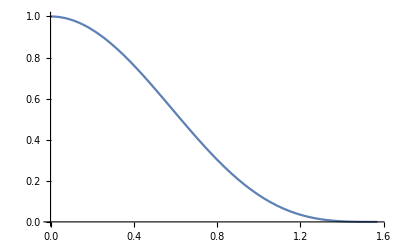

```mathematica
Plot[Cos[x]^(d/2+1/2 √(d^2+4 L^2 m^2)) JacobiP[j,d/2-1,1/2 √(d^2+4 L^2 m^2),Cos[2x]]/.j->0/.d->3/.m->1/.L->1,{x,0,π/2},PlotRange->All]
```